```mathematica
Grid[{{"Le Coniche",-Graphics-}},ItemStyle->{Automatic,{1->{FontFamily->"Roboto Condensed",FontSize->20}}},Frame-> None,FrameStyle->{RGBColor[0.94,0.94,0.94]},Alignment->{{Left,Right}},Spacings->10,ItemSize-> Fit]
Grid[{{-Graphics-, Column[{Style["Progetto D'Esame:"],"Matematica Computazionale (LM Informatica)\nCalcolo Numerico e Software Didattico (LM Matematica)","Aliona \nLoredana\nYuan\nCarlo\nSimone"},Frame->None,Spacings->1]}}, ItemSize->Fit, Frame->None, Alignment->{{Right, Left}},Spacings->3, ItemStyle->{Automatic, {1-> {FontFamily->"Roboto Condensed", FontSize-> 18}}}]
```

Le Coniche | -Graphics-

-Graphics- | Progetto D'Esame:
Matematica Computazionale (LM Informatica)
Calcolo Numerico e Software Didattico (LM Matematica)
Aliona 
Loredana
Yuan
Carlo
Simone

```mathematica
SetDirectory[NotebookDirectory[]]; (* imposto la cartella attuale come base in cui cercare i file *)
Get["PackageProgetto`"];(* aggiungere once quando abbiamo finito il package perchè se no non lo ricarica*)
```

```mathematica
rFile["exercices/first.txt"]
```

### Second level section heading

Text lorem ipsum dolor sit amet, consectetuer adipiscing elit, sed diam nonummy nibh euismod tincidunt ut laoreet dolore magna aliquam erat volutpat. Ut wisi enim ad minim veniam, quis nostrud exerci tation ullamcorper suscipit lobortis nisl ut aliquip ex ea commodo consequat.

#### Third level section heading

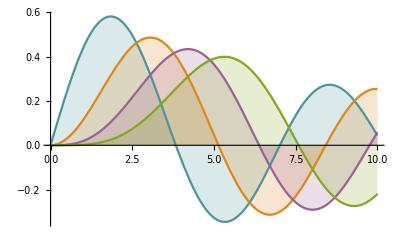

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

### Second level section heading

-Graphics- | SideCaption duis autem vel eum iriure dolor in hendrerit in vulputate velit esse molestie consequat, vel illum dolore eu feugiat nulla facilisis at vero eros et accumsan et iusto odio dignissim qui blandit praesent luptatum zril delenit augue duis dolore te feugait nulla facilisi.